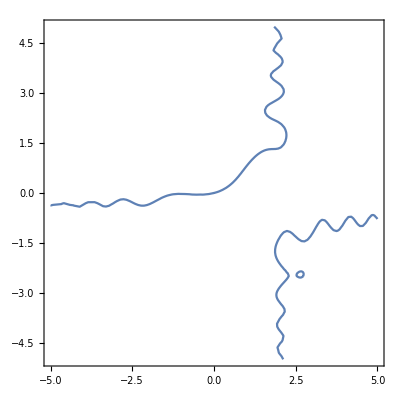

```mathematica
ContourPlot[Sin[x^2]+2x*y+Cos[y^2]+x-4y==1,{x,-5,5},{y,-5,5}]
```

```mathematica
D[Sin[x^2]+2x*y+Cos[y^2]+x-4y==1,{y,2},NonConstants->{x}]
```

```mathematica
D[Sin[x[y]*x[y]]+2x[y]*y+Cos[y^2]+x[y]-4y==1,{y,2},x[y]]
```

-12 Sin[x[y]^2] x[y] x'[y]^2-8 Cos[x[y]^2] x[y]^3 x'[y]^2+2 Cos[x[y]^2] x''[y]-4 Sin[x[y]^2] x[y]^2 x''[y]==0

```mathematica
Solve[D[Sin[x[y]*x[y]]+2x[y]*y+Cos[y^2]+x[y]-4y==1,{y,2}],x''[y]]/.{y->0, x[y]-> 0, x'[y]->4}
```

{{x''[0]→-48}}

```mathematica
Solve[D[Sin[x[y]*x[y]]+2x[y]*y+Cos[y^2]+x[y]-4y==1,{y,2}],x''[y]]
```

{{x''[y]→(2 (2 y^2 Cos[y^2]+Sin[y^2]-2 x'[y]-Cos[x[y]^2] x'[y]^2+2 Sin[x[y]^2] x[y]^2 x'[y]^2))/(1+2 y+2 Cos[x[y]^2] x[y])}}

```mathematica
f[c_]=HoldForm[Solve[D[Sin[x[y]*x[y]]+2x[y]*y+Cos[y^2]+x[y]-4y==1,{y,c}],D[x[y],{y,c}]]]
```

Solve[∂_{y,c} (Sin[x[y] x[y]]+2 x[y] y+Cos[y^2]+x[y]-4 y==1),∂_{y,c} x[y]]

```mathematica
ReleaseHold[f[1]]
```

{{x'[y]→(2 (2+y Sin[y^2]-x[y]))/(1+2 y+2 Cos[x[y]^2] x[y])}}

```mathematica
ReleaseHold[f[2]]
```

{{x''[y]→(2 (2 y^2 Cos[y^2]+Sin[y^2]-2 x'[y]-Cos[x[y]^2] x'[y]^2+2 Sin[x[y]^2] x[y]^2 x'[y]^2))/(1+2 y+2 Cos[x[y]^2] x[y])}}

```mathematica
ReleaseHold[f[3]]//.y->0
```

{{x^(3)[0]→-((2 (-6 Sin[x[0]^2] x[0] x'[0]^3-4 Cos[x[0]^2] x[0]^3 x'[0]^3+3 x''[0]+3 Cos[x[0]^2] x'[0] x''[0]-6 Sin[x[0]^2] x[0]^2 x'[0] x''[0]))/(1+2 Cos[x[0]^2] x[0]))}}

```mathematica
ReleaseHold[f[4]]
```

{{x^(4)[y]→-1/(1+2 y+2 Cos[x[y]^2] x[y])2 (-6 Cos[y^2]+8 y^4 Cos[y^2]+24 y^2 Sin[y^2]-6 Sin[x[y]^2] x'[y]^4-24 Cos[x[y]^2] x[y]^2 x'[y]^4+8 Sin[x[y]^2] x[y]^4 x'[y]^4-36 Sin[x[y]^2] x[y] x'[y]^2 x''[y]-24 Cos[x[y]^2] x[y]^3 x'[y]^2 x''[y]+3 Cos[x[y]^2] x''[y]^2-6 Sin[x[y]^2] x[y]^2 x''[y]^2+4 x^(3)[y]+4 Cos[x[y]^2] x'[y] x^(3)[y]-8 Sin[x[y]^2] x[y]^2 x'[y] x^(3)[y])}}

```mathematica
derivatives=List[]
```

{}

```mathematica
For[i=1,i≤10,i++,
AppendTo[derivatives,ReleaseHold[f[i]]]

];
```

Solve::ivar: (1+(√2 y)/(√(y^2)))/(2 √(y+√2 √(y^2)))[y]+√(y+√2 √(y^2))'[y] is not a valid variable.

Solve::ivar: (-(1+(√2 y)/(√Power[«2»]))^2/(4 (y+√2 √Power[«2»])^(3/2))+(-(√2 y^2)/((y^2)^(3/2))+(√2)/(√(y^2)))/(2 √(y+√2 √Power[«2»])))[y]+2 ((1+(√2 y)/(√Power[«2»]))/(2 √(y+Power[«2»] Power[«2»])))'[y]+√(y+√2 √(y^2))''[y] is not a valid variable.

Solve::ivar: … is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

```mathematica
derivatives=ReplacePart[derivatives,1->{{x'[0]->{{4}}}}];
```

```mathematica
For[z=2,z≤10,z++,

For[d=1,d<z,d++,
derivatives=ReplacePart[derivatives,z->ReplaceAll[Extract[derivatives,z],{D[x[y],{y,d}]->{Extract[<|Extract[derivatives,d]|>,{Key[D[x[y],{y,d}]/.y->0],1}]},y->0,x[y]->0}]];

];
];
```

Power::infy: Infinite expression 1/(√0) encountered.

Infinity::indet: Indeterminate expression 0 √2 ComplexInfinity encountered.

Power::infy: Infinite expression 1/(√0) encountered.

Extract::keyw: Key Indeterminate[0] does not exist in <|√(y+√2 √(y^2))'[0]→{{4}}|>.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0 √2 ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

Solve::ivar: Indeterminate is not a valid variable.

Extract::keyw: Key Indeterminate[0] does not exist in <|√(y+√2 √(y^2))'[0]→{{4}}|>.

Solve::ivar: Indeterminate is not a valid variable.

Extract::pspec1: Part specification Key[Indeterminate] is not applicable.

Extract::pspec1: Part specification Key[Indeterminate[0]] is not applicable.

Solve::ivar: Indeterminate is not a valid variable.

General::stop: Further output of Solve::ivar will be suppressed during this calculation.

Extract::pspec1: Part specification Key[Indeterminate] is not applicable.

General::stop: Further output of Extract::pspec1 will be suppressed during this calculation.

```mathematica
derivatives
```

{{{x'[y]→(2 (2+y Sin[y^2]-x[y]))/(1+2 y+2 Cos[x[y]^2] x[y])}},{{x''[y]→(2 (2 y^2 Cos[y^2]+Sin[y^2]-2 x'[y]-Cos[x[y]^2] x'[y]^2+2 Sin[x[y]^2] x[y]^2 x'[y]^2))/(1+2 y+2 Cos[x[y]^2] x[y])}},{{x^(3)[y]→-((2 (-6 y Cos[y^2]+4 y^3 Sin[y^2]-6 Sin[x[y]^2] x[y] x'[y]^3-4 Cos[x[y]^2] x[y]^3 x'[y]^3+3 x''[y]+3 Cos[x[y]^2] x'[y] x''[y]-6 Sin[x[y]^2] x[y]^2 x'[y] x''[y]))/(1+2 y+2 Cos[x[y]^2] x[y]))}},{{x^(4)[y]→-((2 (-6 Cos[y^2]+8 y^4 Cos[y^2]+24 y^2 Sin[y^2]-6 Sin[x[y]^2] x'[y]^4-24 Cos[x[y]^2] x[y]^2 x'[y]^4+8 Sin[x[y]^2] x[y]^4 x'[y]^4-36 Sin[x[y]^2] x[y] x'[y]^2 x''[y]-24 Cos[x[y]^2] x[y]^3 x'[y]^2 x''[y]+3 Cos[x[y]^2] x''[y]^2-6 Sin[x[y]^2] x[y]^2 x''[y]^2+4 x^(3)[y]+4 Cos[x[y]^2] x'[y] x^(3)[y]-8 Sin[x[y]^2] x[y]^2 x'[y] x^(3)[y]))/(1+2 y+2 Cos[x[y]^2] x[y]))}},{{x^(5)[y]→(2 (-80 y^3 Cos[y^2]-60 y Sin[y^2]+16 y^5 Sin[y^2]+60 Cos[x[y]^2] x[y] x'[y]^5-80 Sin[x[y]^2] x[y]^3 x'[y]^5-16 Cos[x[y]^2] x[y]^5 x'[y]^5+60 Sin[x[y]^2] x'[y]^3 x''[y]+240 Cos[x[y]^2] x[y]^2 x'[y]^3 x''[y]-80 Sin[x[y]^2] x[y]^4 x'[y]^3 x''[y]+90 Sin[x[y]^2] x[y] x'[y] x''[y]^2+60 Cos[x[y]^2] x[y]^3 x'[y] x''[y]^2+60 Sin[x[y]^2] x[y] x'[y]^2 x^(3)[y]+40 Cos[x[y]^2] x[y]^3 x'[y]^2 x^(3)[y]-10 Cos[x[y]^2] x''[y] x^(3)[y]+20 Sin[x[y]^2] x[y]^2 x''[y] x^(3)[y]-5 x^(4)[y]-5 Cos[x[y]^2] x'[y] x^(4)[y]+10 Sin[x[y]^2] x[y]^2 x'[y] x^(4)[y]))/(1+2 y+2 Cos[x[y]^2] x[y])}},{{x^(6)[y]→(2 (-360 y^2 Cos[y^2]+32 y^6 Cos[y^2]-60 Sin[y^2]+240 y^4 Sin[y^2]+60 Cos[x[y]^2] x'[y]^6-360 Sin[x[y]^2] x[y]^2 x'[y]^6-240 Cos[x[y]^2] x[y]^4 x'[y]^6+32 Sin[x[y]^2] x[y]^6 x'[y]^6+900 Cos[x[y]^2] x[y] x'[y]^4 x''[y]-1200 Sin[x[y]^2] x[y]^3 x'[y]^4 x''[y]-240 Cos[x[y]^2] x[y]^5 x'[y]^4 x''[y]+270 Sin[x[y]^2] x'[y]^2 x''[y]^2+1080 Cos[x[y]^2] x[y]^2 x'[y]^2 x''[y]^2-360 Sin[x[y]^2] x[y]^4 x'[y]^2 x''[y]^2+90 Sin[x[y]^2] x[y] x''[y]^3+60 Cos[x[y]^2] x[y]^3 x''[y]^3+120 Sin[x[y]^2] x'[y]^3 x^(3)[y]+480 Cos[x[y]^2] x[y]^2 x'[y]^3 x^(3)[y]-160 Sin[x[y]^2] x[y]^4 x'[y]^3 x^(3)[y]+360 Sin[x[y]^2] x[y] x'[y] x''[y] x^(3)[y]+240 Cos[x[y]^2] x[y]^3 x'[y] x''[y] x^(3)[y]-10 Cos[x[y]^2] (x^(3)[y])^2+20 Sin[x[y]^2] x[y]^2 (x^(3)[y])^2+90 Sin[x[y]^2] x[y] x'[y]^2 x^(4)[y]+60 Cos[x[y]^2] x[y]^3 x'[y]^2 x^(4)[y]-15 Cos[x[y]^2] x''[y] x^(4)[y]+30 Sin[x[y]^2] x[y]^2 x''[y] x^(4)[y]-6 x^(5)[y]-6 Cos[x[y]^2] x'[y] x^(5)[y]+12 Sin[x[y]^2] x[y]^2 x'[y] x^(5)[y]))/(1+2 y+2 Cos[x[y]^2] x[y])}},{{x^(7)[y]→-((2 (840 y Cos[y^2]-672 y^5 Cos[y^2]-1680 y^3 Sin[y^2]+64 y^7 Sin[y^2]+840 Sin[x[y]^2] x[y] x'[y]^7+1680 Cos[x[y]^2] x[y]^3 x'[y]^7-672 Sin[x[y]^2] x[y]^5 x'[y]^7-64 Cos[x[y]^2] x[y]^7 x'[y]^7-1260 Cos[x[y]^2] x'[y]^5 x''[y]+7560 Sin[x[y]^2] x[y]^2 x'[y]^5 x''[y]+5040 Cos[x[y]^2] x[y]^4 x'[y]^5 x''[y]-672 Sin[x[y]^2] x[y]^6 x'[y]^5 x''[y]-6300 Cos[x[y]^2] x[y] x'[y]^3 x''[y]^2+8400 Sin[x[y]^2] x[y]^3 x'[y]^3 x''[y]^2+1680 Cos[x[y]^2] x[y]^5 x'[y]^3 x''[y]^2-630 Sin[x[y]^2] x'[y] x''[y]^3-2520 Cos[x[y]^2] x[y]^2 x'[y] x''[y]^3+840 Sin[x[y]^2] x[y]^4 x'[y] x''[y]^3-2100 Cos[x[y]^2] x[y] x'[y]^4 x^(3)[y]+2800 Sin[x[y]^2] x[y]^3 x'[y]^4 x^(3)[y]+560 Cos[x[y]^2] x[y]^5 x'[y]^4 x^(3)[y]-1260 Sin[x[y]^2] x'[y]^2 x''[y] x^(3)[y]-5040 Cos[x[y]^2] x[y]^2 x'[y]^2 x''[y] x^(3)[y]+1680 Sin[x[y]^2] x[y]^4 x'[y]^2 x''[y] x^(3)[y]-630 Sin[x[y]^2] x[y] x''[y]^2 x^(3)[y]-420 Cos[x[y]^2] x[y]^3 x''[y]^2 x^(3)[y]-420 Sin[x[y]^2] x[y] x'[y] (x^(3)[y])^2-280 Cos[x[y]^2] x[y]^3 x'[y] (x^(3)[y])^2-210 Sin[x[y]^2] x'[y]^3 x^(4)[y]-840 Cos[x[y]^2] x[y]^2 x'[y]^3 x^(4)[y]+280 Sin[x[y]^2] x[y]^4 x'[y]^3 x^(4)[y]-630 Sin[x[y]^2] x[y] x'[y] x''[y] x^(4)[y]-420 Cos[x[y]^2] x[y]^3 x'[y] x''[y] x^(4)[y]+35 Cos[x[y]^2] x^(3)[y] x^(4)[y]-70 Sin[x[y]^2] x[y]^2 x^(3)[y] x^(4)[y]-126 Sin[x[y]^2] x[y] x'[y]^2 x^(5)[y]-84 Cos[x[y]^2] x[y]^3 x'[y]^2 x^(5)[y]+21 Cos[x[y]^2] x''[y] x^(5)[y]-42 Sin[x[y]^2] x[y]^2 x''[y] x^(5)[y]+7 x^(6)[y]+7 Cos[x[y]^2] x'[y] x^(6)[y]-14 Sin[x[y]^2] x[y]^2 x'[y] x^(6)[y]))/(1+2 y+2 Cos[x[y]^2] x[y]))}},{{x^(8)[y]→-((2 (840 Cos[y^2]-6720 y^4 Cos[y^2]+128 y^8 Cos[y^2]-6720 y^2 Sin[y^2]+1792 y^6 Sin[y^2]+840 Sin[x[y]^2] x'[y]^8+6720 Cos[x[y]^2] x[y]^2 x'[y]^8-6720 Sin[x[y]^2] x[y]^4 x'[y]^8-1792 Cos[x[y]^2] x[y]^6 x'[y]^8+128 Sin[x[y]^2] x[y]^8 x'[y]^8+23520 Sin[x[y]^2] x[y] x'[y]^6 x''[y]+47040 Cos[x[y]^2] x[y]^3 x'[y]^6 x''[y]-18816 Sin[x[y]^2] x[y]^5 x'[y]^6 x''[y]-1792 Cos[x[y]^2] x[y]^7 x'[y]^6 x''[y]-12600 Cos[x[y]^2] x'[y]^4 x''[y]^2+75600 Sin[x[y]^2] x[y]^2 x'[y]^4 x''[y]^2+50400 Cos[x[y]^2] x[y]^4 x'[y]^4 x''[y]^2-6720 Sin[x[y]^2] x[y]^6 x'[y]^4 x''[y]^2-25200 Cos[x[y]^2] x[y] x'[y]^2 x''[y]^3+33600 Sin[x[y]^2] x[y]^3 x'[y]^2 x''[y]^3+6720 Cos[x[y]^2] x[y]^5 x'[y]^2 x''[y]^3-630 Sin[x[y]^2] x''[y]^4-2520 Cos[x[y]^2] x[y]^2 x''[y]^4+840 Sin[x[y]^2] x[y]^4 x''[y]^4-3360 Cos[x[y]^2] x'[y]^5 x^(3)[y]+20160 Sin[x[y]^2] x[y]^2 x'[y]^5 x^(3)[y]+13440 Cos[x[y]^2] x[y]^4 x'[y]^5 x^(3)[y]-1792 Sin[x[y]^2] x[y]^6 x'[y]^5 x^(3)[y]-33600 Cos[x[y]^2] x[y] x'[y]^3 x''[y] x^(3)[y]+44800 Sin[x[y]^2] x[y]^3 x'[y]^3 x''[y] x^(3)[y]+8960 Cos[x[y]^2] x[y]^5 x'[y]^3 x''[y] x^(3)[y]-5040 Sin[x[y]^2] x'[y] x''[y]^2 x^(3)[y]-20160 Cos[x[y]^2] x[y]^2 x'[y] x''[y]^2 x^(3)[y]+6720 Sin[x[y]^2] x[y]^4 x'[y] x''[y]^2 x^(3)[y]-1680 Sin[x[y]^2] x'[y]^2 (x^(3)[y])^2-6720 Cos[x[y]^2] x[y]^2 x'[y]^2 (x^(3)[y])^2+2240 Sin[x[y]^2] x[y]^4 x'[y]^2 (x^(3)[y])^2-1680 Sin[x[y]^2] x[y] x''[y] (x^(3)[y])^2-1120 Cos[x[y]^2] x[y]^3 x''[y] (x^(3)[y])^2-4200 Cos[x[y]^2] x[y] x'[y]^4 x^(4)[y]+5600 Sin[x[y]^2] x[y]^3 x'[y]^4 x^(4)[y]+1120 Cos[x[y]^2] x[y]^5 x'[y]^4 x^(4)[y]-2520 Sin[x[y]^2] x'[y]^2 x''[y] x^(4)[y]-10080 Cos[x[y]^2] x[y]^2 x'[y]^2 x''[y] x^(4)[y]+3360 Sin[x[y]^2] x[y]^4 x'[y]^2 x''[y] x^(4)[y]-1260 Sin[x[y]^2] x[y] x''[y]^2 x^(4)[y]-840 Cos[x[y]^2] x[y]^3 x''[y]^2 x^(4)[y]-1680 Sin[x[y]^2] x[y] x'[y] x^(3)[y] x^(4)[y]-1120 Cos[x[y]^2] x[y]^3 x'[y] x^(3)[y] x^(4)[y]+35 Cos[x[y]^2] (x^(4)[y])^2-70 Sin[x[y]^2] x[y]^2 (x^(4)[y])^2-336 Sin[x[y]^2] x'[y]^3 x^(5)[y]-1344 Cos[x[y]^2] x[y]^2 x'[y]^3 x^(5)[y]+448 Sin[x[y]^2] x[y]^4 x'[y]^3 x^(5)[y]-1008 Sin[x[y]^2] x[y] x'[y] x''[y] x^(5)[y]-672 Cos[x[y]^2] x[y]^3 x'[y] x''[y] x^(5)[y]+56 Cos[x[y]^2] x^(3)[y] x^(5)[y]-112 Sin[x[y]^2] x[y]^2 x^(3)[y] x^(5)[y]-168 Sin[x[y]^2] x[y] x'[y]^2 x^(6)[y]-112 Cos[x[y]^2] x[y]^3 x'[y]^2 x^(6)[y]+28 Cos[x[y]^2] x''[y] x^(6)[y]-56 Sin[x[y]^2] x[y]^2 x''[y] x^(6)[y]+8 x^(7)[y]+8 Cos[x[y]^2] x'[y] x^(7)[y]-16 Sin[x[y]^2] x[y]^2 x'[y] x^(7)[y]))/(1+2 y+2 Cos[x[y]^2] x[y]))}},{{x^(9)[y]→(2 (40320 y^3 Cos[y^2]-4608 y^7 Cos[y^2]+15120 y Sin[y^2]-24192 y^5 Sin[y^2]+256 y^9 Sin[y^2]-15120 Cos[x[y]^2] x[y] x'[y]^9+40320 Sin[x[y]^2] x[y]^3 x'[y]^9+24192 Cos[x[y]^2] x[y]^5 x'[y]^9-4608 Sin[x[y]^2] x[y]^7 x'[y]^9-256 Cos[x[y]^2] x[y]^9 x'[y]^9-30240 Sin[x[y]^2] x'[y]^7 x''[y]-241920 Cos[x[y]^2] x[y]^2 x'[y]^7 x''[y]+241920 Sin[x[y]^2] x[y]^4 x'[y]^7 x''[y]+64512 Cos[x[y]^2] x[y]^6 x'[y]^7 x''[y]-4608 Sin[x[y]^2] x[y]^8 x'[y]^7 x''[y]-317520 Sin[x[y]^2] x[y] x'[y]^5 x''[y]^2-635040 Cos[x[y]^2] x[y]^3 x'[y]^5 x''[y]^2+254016 Sin[x[y]^2] x[y]^5 x'[y]^5 x''[y]^2+24192 Cos[x[y]^2] x[y]^7 x'[y]^5 x''[y]^2+75600 Cos[x[y]^2] x'[y]^3 x''[y]^3-453600 Sin[x[y]^2] x[y]^2 x'[y]^3 x''[y]^3-302400 Cos[x[y]^2] x[y]^4 x'[y]^3 x''[y]^3+40320 Sin[x[y]^2] x[y]^6 x'[y]^3 x''[y]^3+56700 Cos[x[y]^2] x[y] x'[y] x''[y]^4-75600 Sin[x[y]^2] x[y]^3 x'[y] x''[y]^4-15120 Cos[x[y]^2] x[y]^5 x'[y] x''[y]^4-70560 Sin[x[y]^2] x[y] x'[y]^6 x^(3)[y]-141120 Cos[x[y]^2] x[y]^3 x'[y]^6 x^(3)[y]+56448 Sin[x[y]^2] x[y]^5 x'[y]^6 x^(3)[y]+5376 Cos[x[y]^2] x[y]^7 x'[y]^6 x^(3)[y]+75600 Cos[x[y]^2] x'[y]^4 x''[y] x^(3)[y]-453600 Sin[x[y]^2] x[y]^2 x'[y]^4 x''[y] x^(3)[y]-302400 Cos[x[y]^2] x[y]^4 x'[y]^4 x''[y] x^(3)[y]+40320 Sin[x[y]^2] x[y]^6 x'[y]^4 x''[y] x^(3)[y]+226800 Cos[x[y]^2] x[y] x'[y]^2 x''[y]^2 x^(3)[y]-302400 Sin[x[y]^2] x[y]^3 x'[y]^2 x''[y]^2 x^(3)[y]-60480 Cos[x[y]^2] x[y]^5 x'[y]^2 x''[y]^2 x^(3)[y]+7560 Sin[x[y]^2] x''[y]^3 x^(3)[y]+30240 Cos[x[y]^2] x[y]^2 x''[y]^3 x^(3)[y]-10080 Sin[x[y]^2] x[y]^4 x''[y]^3 x^(3)[y]+50400 Cos[x[y]^2] x[y] x'[y]^3 (x^(3)[y])^2-67200 Sin[x[y]^2] x[y]^3 x'[y]^3 (x^(3)[y])^2-13440 Cos[x[y]^2] x[y]^5 x'[y]^3 (x^(3)[y])^2+15120 Sin[x[y]^2] x'[y] x''[y] (x^(3)[y])^2+60480 Cos[x[y]^2] x[y]^2 x'[y] x''[y] (x^(3)[y])^2-20160 Sin[x[y]^2] x[y]^4 x'[y] x''[y] (x^(3)[y])^2+1680 Sin[x[y]^2] x[y] (x^(3)[y])^3+1120 Cos[x[y]^2] x[y]^3 (x^(3)[y])^3+7560 Cos[x[y]^2] x'[y]^5 x^(4)[y]-45360 Sin[x[y]^2] x[y]^2 x'[y]^5 x^(4)[y]-30240 Cos[x[y]^2] x[y]^4 x'[y]^5 x^(4)[y]+4032 Sin[x[y]^2] x[y]^6 x'[y]^5 x^(4)[y]+75600 Cos[x[y]^2] x[y] x'[y]^3 x''[y] x^(4)[y]-100800 Sin[x[y]^2] x[y]^3 x'[y]^3 x''[y] x^(4)[y]-20160 Cos[x[y]^2] x[y]^5 x'[y]^3 x''[y] x^(4)[y]+11340 Sin[x[y]^2] x'[y] x''[y]^2 x^(4)[y]+45360 Cos[x[y]^2] x[y]^2 x'[y] x''[y]^2 x^(4)[y]-15120 Sin[x[y]^2] x[y]^4 x'[y] x''[y]^2 x^(4)[y]+7560 Sin[x[y]^2] x'[y]^2 x^(3)[y] x^(4)[y]+30240 Cos[x[y]^2] x[y]^2 x'[y]^2 x^(3)[y] x^(4)[y]-10080 Sin[x[y]^2] x[y]^4 x'[y]^2 x^(3)[y] x^(4)[y]+7560 Sin[x[y]^2] x[y] x''[y] x^(3)[y] x^(4)[y]+5040 Cos[x[y]^2] x[y]^3 x''[y] x^(3)[y] x^(4)[y]+1890 Sin[x[y]^2] x[y] x'[y] (x^(4)[y])^2+1260 Cos[x[y]^2] x[y]^3 x'[y] (x^(4)[y])^2+7560 Cos[x[y]^2] x[y] x'[y]^4 x^(5)[y]-10080 Sin[x[y]^2] x[y]^3 x'[y]^4 x^(5)[y]-2016 Cos[x[y]^2] x[y]^5 x'[y]^4 x^(5)[y]+4536 Sin[x[y]^2] x'[y]^2 x''[y] x^(5)[y]+18144 Cos[x[y]^2] x[y]^2 x'[y]^2 x''[y] x^(5)[y]-6048 Sin[x[y]^2] x[y]^4 x'[y]^2 x''[y] x^(5)[y]+2268 Sin[x[y]^2] x[y] x''[y]^2 x^(5)[y]+1512 Cos[x[y]^2] x[y]^3 x''[y]^2 x^(5)[y]+3024 Sin[x[y]^2] x[y] x'[y] x^(3)[y] x^(5)[y]+2016 Cos[x[y]^2] x[y]^3 x'[y] x^(3)[y] x^(5)[y]-126 Cos[x[y]^2] x^(4)[y] x^(5)[y]+252 Sin[x[y]^2] x[y]^2 x^(4)[y] x^(5)[y]+504 Sin[x[y]^2] x'[y]^3 x^(6)[y]+2016 Cos[x[y]^2] x[y]^2 x'[y]^3 x^(6)[y]-672 Sin[x[y]^2] x[y]^4 x'[y]^3 x^(6)[y]+1512 Sin[x[y]^2] x[y] x'[y] x''[y] x^(6)[y]+1008 Cos[x[y]^2] x[y]^3 x'[y] x''[y] x^(6)[y]-84 Cos[x[y]^2] x^(3)[y] x^(6)[y]+168 Sin[x[y]^2] x[y]^2 x^(3)[y] x^(6)[y]+216 Sin[x[y]^2] x[y] x'[y]^2 x^(7)[y]+144 Cos[x[y]^2] x[y]^3 x'[y]^2 x^(7)[y]-36 Cos[x[y]^2] x''[y] x^(7)[y]+72 Sin[x[y]^2] x[y]^2 x''[y] x^(7)[y]-9 x^(8)[y]-9 Cos[x[y]^2] x'[y] x^(8)[y]+18 Sin[x[y]^2] x[y]^2 x'[y] x^(8)[y]))/(1+2 y+2 Cos[x[y]^2] x[y])}},{{x^(10)[y]→(2 (151200 y^2 Cos[y^2]-80640 y^6 Cos[y^2]+512 y^10 Cos[y^2]+15120 Sin[y^2]-201600 y^4 Sin[y^2]+11520 y^8 Sin[y^2]-15120 Cos[x[y]^2] x'[y]^10+151200 Sin[x[y]^2] x[y]^2 x'[y]^10+201600 Cos[x[y]^2] x[y]^4 x'[y]^10-80640 Sin[x[y]^2] x[y]^6 x'[y]^10-11520 Cos[x[y]^2] x[y]^8 x'[y]^10+512 Sin[x[y]^2] x[y]^10 x'[y]^10-680400 Cos[x[y]^2] x[y] x'[y]^8 x''[y]+1814400 Sin[x[y]^2] x[y]^3 x'[y]^8 x''[y]+1088640 Cos[x[y]^2] x[y]^5 x'[y]^8 x''[y]-207360 Sin[x[y]^2] x[y]^7 x'[y]^8 x''[y]-11520 Cos[x[y]^2] x[y]^9 x'[y]^8 x''[y]-529200 Sin[x[y]^2] x'[y]^6 x''[y]^2-4233600 Cos[x[y]^2] x[y]^2 x'[y]^6 x''[y]^2+4233600 Sin[x[y]^2] x[y]^4 x'[y]^6 x''[y]^2+1128960 Cos[x[y]^2] x[y]^6 x'[y]^6 x''[y]^2-80640 Sin[x[y]^2] x[y]^8 x'[y]^6 x''[y]^2-2646000 Sin[x[y]^2] x[y] x'[y]^4 x''[y]^3-5292000 Cos[x[y]^2] x[y]^3 x'[y]^4 x''[y]^3+2116800 Sin[x[y]^2] x[y]^5 x'[y]^4 x''[y]^3+201600 Cos[x[y]^2] x[y]^7 x'[y]^4 x''[y]^3+283500 Cos[x[y]^2] x'[y]^2 x''[y]^4-1701000 Sin[x[y]^2] x[y]^2 x'[y]^2 x''[y]^4-1134000 Cos[x[y]^2] x[y]^4 x'[y]^2 x''[y]^4+151200 Sin[x[y]^2] x[y]^6 x'[y]^2 x''[y]^4+56700 Cos[x[y]^2] x[y] x''[y]^5-75600 Sin[x[y]^2] x[y]^3 x''[y]^5-15120 Cos[x[y]^2] x[y]^5 x''[y]^5-100800 Sin[x[y]^2] x'[y]^7 x^(3)[y]-806400 Cos[x[y]^2] x[y]^2 x'[y]^7 x^(3)[y]+806400 Sin[x[y]^2] x[y]^4 x'[y]^7 x^(3)[y]+215040 Cos[x[y]^2] x[y]^6 x'[y]^7 x^(3)[y]-15360 Sin[x[y]^2] x[y]^8 x'[y]^7 x^(3)[y]-2116800 Sin[x[y]^2] x[y] x'[y]^5 x''[y] x^(3)[y]-4233600 Cos[x[y]^2] x[y]^3 x'[y]^5 x''[y] x^(3)[y]+1693440 Sin[x[y]^2] x[y]^5 x'[y]^5 x''[y] x^(3)[y]+161280 Cos[x[y]^2] x[y]^7 x'[y]^5 x''[y] x^(3)[y]+756000 Cos[x[y]^2] x'[y]^3 x''[y]^2 x^(3)[y]-4536000 Sin[x[y]^2] x[y]^2 x'[y]^3 x''[y]^2 x^(3)[y]-3024000 Cos[x[y]^2] x[y]^4 x'[y]^3 x''[y]^2 x^(3)[y]+403200 Sin[x[y]^2] x[y]^6 x'[y]^3 x''[y]^2 x^(3)[y]+756000 Cos[x[y]^2] x[y] x'[y] x''[y]^3 x^(3)[y]-1008000 Sin[x[y]^2] x[y]^3 x'[y] x''[y]^3 x^(3)[y]-201600 Cos[x[y]^2] x[y]^5 x'[y] x''[y]^3 x^(3)[y]+126000 Cos[x[y]^2] x'[y]^4 (x^(3)[y])^2-756000 Sin[x[y]^2] x[y]^2 x'[y]^4 (x^(3)[y])^2-504000 Cos[x[y]^2] x[y]^4 x'[y]^4 (x^(3)[y])^2+67200 Sin[x[y]^2] x[y]^6 x'[y]^4 (x^(3)[y])^2+756000 Cos[x[y]^2] x[y] x'[y]^2 x''[y] (x^(3)[y])^2-1008000 Sin[x[y]^2] x[y]^3 x'[y]^2 x''[y] (x^(3)[y])^2-201600 Cos[x[y]^2] x[y]^5 x'[y]^2 x''[y] (x^(3)[y])^2+37800 Sin[x[y]^2] x''[y]^2 (x^(3)[y])^2+151200 Cos[x[y]^2] x[y]^2 x''[y]^2 (x^(3)[y])^2-50400 Sin[x[y]^2] x[y]^4 x''[y]^2 (x^(3)[y])^2+16800 Sin[x[y]^2] x'[y] (x^(3)[y])^3+67200 Cos[x[y]^2] x[y]^2 x'[y] (x^(3)[y])^3-22400 Sin[x[y]^2] x[y]^4 x'[y] (x^(3)[y])^3-176400 Sin[x[y]^2] x[y] x'[y]^6 x^(4)[y]-352800 Cos[x[y]^2] x[y]^3 x'[y]^6 x^(4)[y]+141120 Sin[x[y]^2] x[y]^5 x'[y]^6 x^(4)[y]+13440 Cos[x[y]^2] x[y]^7 x'[y]^6 x^(4)[y]+189000 Cos[x[y]^2] x'[y]^4 x''[y] x^(4)[y]-1134000 Sin[x[y]^2] x[y]^2 x'[y]^4 x''[y] x^(4)[y]-756000 Cos[x[y]^2] x[y]^4 x'[y]^4 x''[y] x^(4)[y]+100800 Sin[x[y]^2] x[y]^6 x'[y]^4 x''[y] x^(4)[y]+567000 Cos[x[y]^2] x[y] x'[y]^2 x''[y]^2 x^(4)[y]-756000 Sin[x[y]^2] x[y]^3 x'[y]^2 x''[y]^2 x^(4)[y]-151200 Cos[x[y]^2] x[y]^5 x'[y]^2 x''[y]^2 x^(4)[y]+18900 Sin[x[y]^2] x''[y]^3 x^(4)[y]+75600 Cos[x[y]^2] x[y]^2 x''[y]^3 x^(4)[y]-25200 Sin[x[y]^2] x[y]^4 x''[y]^3 x^(4)[y]+252000 Cos[x[y]^2] x[y] x'[y]^3 x^(3)[y] x^(4)[y]-336000 Sin[x[y]^2] x[y]^3 x'[y]^3 x^(3)[y] x^(4)[y]-67200 Cos[x[y]^2] x[y]^5 x'[y]^3 x^(3)[y] x^(4)[y]+75600 Sin[x[y]^2] x'[y] x''[y] x^(3)[y] x^(4)[y]+302400 Cos[x[y]^2] x[y]^2 x'[y] x''[y] x^(3)[y] x^(4)[y]-100800 Sin[x[y]^2] x[y]^4 x'[y] x''[y] x^(3)[y] x^(4)[y]+12600 Sin[x[y]^2] x[y] (x^(3)[y])^2 x^(4)[y]+8400 Cos[x[y]^2] x[y]^3 (x^(3)[y])^2 x^(4)[y]+9450 Sin[x[y]^2] x'[y]^2 (x^(4)[y])^2+37800 Cos[x[y]^2] x[y]^2 x'[y]^2 (x^(4)[y])^2-12600 Sin[x[y]^2] x[y]^4 x'[y]^2 (x^(4)[y])^2+9450 Sin[x[y]^2] x[y] x''[y] (x^(4)[y])^2+6300 Cos[x[y]^2] x[y]^3 x''[y] (x^(4)[y])^2+15120 Cos[x[y]^2] x'[y]^5 x^(5)[y]-90720 Sin[x[y]^2] x[y]^2 x'[y]^5 x^(5)[y]-60480 Cos[x[y]^2] x[y]^4 x'[y]^5 x^(5)[y]+8064 Sin[x[y]^2] x[y]^6 x'[y]^5 x^(5)[y]+151200 Cos[x[y]^2] x[y] x'[y]^3 x''[y] x^(5)[y]-201600 Sin[x[y]^2] x[y]^3 x'[y]^3 x''[y] x^(5)[y]-40320 Cos[x[y]^2] x[y]^5 x'[y]^3 x''[y] x^(5)[y]+22680 Sin[x[y]^2] x'[y] x''[y]^2 x^(5)[y]+90720 Cos[x[y]^2] x[y]^2 x'[y] x''[y]^2 x^(5)[y]-30240 Sin[x[y]^2] x[y]^4 x'[y] x''[y]^2 x^(5)[y]+15120 Sin[x[y]^2] x'[y]^2 x^(3)[y] x^(5)[y]+60480 Cos[x[y]^2] x[y]^2 x'[y]^2 x^(3)[y] x^(5)[y]-20160 Sin[x[y]^2] x[y]^4 x'[y]^2 x^(3)[y] x^(5)[y]+15120 Sin[x[y]^2] x[y] x''[y] x^(3)[y] x^(5)[y]+10080 Cos[x[y]^2] x[y]^3 x''[y] x^(3)[y] x^(5)[y]+7560 Sin[x[y]^2] x[y] x'[y] x^(4)[y] x^(5)[y]+5040 Cos[x[y]^2] x[y]^3 x'[y] x^(4)[y] x^(5)[y]-126 Cos[x[y]^2] (x^(5)[y])^2+252 Sin[x[y]^2] x[y]^2 (x^(5)[y])^2+12600 Cos[x[y]^2] x[y] x'[y]^4 x^(6)[y]-16800 Sin[x[y]^2] x[y]^3 x'[y]^4 x^(6)[y]-3360 Cos[x[y]^2] x[y]^5 x'[y]^4 x^(6)[y]+7560 Sin[x[y]^2] x'[y]^2 x''[y] x^(6)[y]+30240 Cos[x[y]^2] x[y]^2 x'[y]^2 x''[y] x^(6)[y]-10080 Sin[x[y]^2] x[y]^4 x'[y]^2 x''[y] x^(6)[y]+3780 Sin[x[y]^2] x[y] x''[y]^2 x^(6)[y]+2520 Cos[x[y]^2] x[y]^3 x''[y]^2 x^(6)[y]+5040 Sin[x[y]^2] x[y] x'[y] x^(3)[y] x^(6)[y]+3360 Cos[x[y]^2] x[y]^3 x'[y] x^(3)[y] x^(6)[y]-210 Cos[x[y]^2] x^(4)[y] x^(6)[y]+420 Sin[x[y]^2] x[y]^2 x^(4)[y] x^(6)[y]+720 Sin[x[y]^2] x'[y]^3 x^(7)[y]+2880 Cos[x[y]^2] x[y]^2 x'[y]^3 x^(7)[y]-960 Sin[x[y]^2] x[y]^4 x'[y]^3 x^(7)[y]+2160 Sin[x[y]^2] x[y] x'[y] x''[y] x^(7)[y]+1440 Cos[x[y]^2] x[y]^3 x'[y] x''[y] x^(7)[y]-120 Cos[x[y]^2] x^(3)[y] x^(7)[y]+240 Sin[x[y]^2] x[y]^2 x^(3)[y] x^(7)[y]+270 Sin[x[y]^2] x[y] x'[y]^2 x^(8)[y]+180 Cos[x[y]^2] x[y]^3 x'[y]^2 x^(8)[y]-45 Cos[x[y]^2] x''[y] x^(8)[y]+90 Sin[x[y]^2] x[y]^2 x''[y] x^(8)[y]-10 x^(9)[y]-10 Cos[x[y]^2] x'[y] x^(9)[y]+20 Sin[x[y]^2] x[y]^2 x'[y] x^(9)[y]))/(1+2 y+2 Cos[x[y]^2] x[y])}}}

```mathematica
derivatives=ReplacePart[derivatives,3->Extract[derivatives,3]/.{y->0,x[y]->0,D[x[y],{y,2}]->5}];
```

```mathematica
Extract[<|Extract[derivatives,1]|>,{Key[D[x[y],{y,1}]/.{y->0}],1}]
```

{4}

```mathematica
derivatives=ReplacePart[derivatives,3->Extract[<|Extract[derivatives,3]|>,{Key[D[x[y],{y,3}]/.{y->0}],1}]//.{{D[x[y],{y,2}]}->{Extract[<|Extract[derivatives,2]|>,{Key[D[x[y],{y,2}]/.{y->0}],1}]},y->0,x[y]->0}];
```

Extract::pspec1: Part specification Key[x^(3)[0]] is not applicable.

```mathematica
derivatives=ReplacePart[derivatives,3->Evaluate[Extract[<|Extract[derivatives,3]|>,{Key[D[x[y],{y,3}]/.{y->0}],1}]//.D[x[y],{y,d}]->{Extract[<|Extract[derivatives,2]|>,{Key[D[x[y],{y,2}]/.{y->0}],1}]}]]
```

{{{x'[0]→{{4}}}},{{x''[0]→{{-48}}}},{-30 x''[0]},{{x^(4)[0]→{{-2 (-6+3 x''[0]^2+20 x^(3)[0])}}}},{{x^(5)[0]→{{2 (-10 x''[0] x^(3)[0]-25 x^(4)[0])}}}},{{x^(6)[0]→{{2 (245760-10 (x^(3)[0])^2-15 x''[0] x^(4)[0]-30 x^(5)[0])}}}},{{x^(7)[0]→{{-2 (-1290240 x''[0]+35 x^(3)[0] x^(4)[0]+21 x''[0] x^(5)[0]+35 x^(6)[0])}}}},{{x^(8)[0]→{{-2 (840-3225600 x''[0]^2-3440640 x^(3)[0]+35 (x^(4)[0])^2+56 x^(3)[0] x^(5)[0]+28 x''[0] x^(6)[0]+40 x^(7)[0])}}}},{{x^(9)[0]→{{2 (4838400 x''[0]^3+19353600 x''[0] x^(3)[0]+7741440 x^(4)[0]-126 x^(4)[0] x^(5)[0]-84 x^(3)[0] x^(6)[0]-36 x''[0] x^(7)[0]-45 x^(8)[0])}}}},{{x^(10)[0]→{{2 (-15854469120+4536000 x''[0]^4+48384000 x''[0]^2 x^(3)[0]+32256000 (x^(3)[0])^2+48384000 x''[0] x^(4)[0]+15482880 x^(5)[0]-126 (x^(5)[0])^2-210 x^(4)[0] x^(6)[0]-120 x^(3)[0] x^(7)[0]-45 x''[0] x^(8)[0]-50 x^(9)[0])}}}}}

{4}

```mathematica
D[x[y],{y,2}]/.{y->0}
```

x''[0]

```mathematica
derivatives
```

{x'[0]→4,x''[0]→{{-48}},x^(3)[0]→-30 x''[0],x^(4)[0]→-2 (-6+3 x''[0]^2+20 x^(3)[0]),x^(5)[0]→2 (-10 x''[0] x^(3)[0]-25 x^(4)[0]),x^(6)[0]→2 (245760-10 (x^(3)[0])^2-15 x''[0] x^(4)[0]-30 x^(5)[0]),x^(7)[0]→-2 (-1290240 x''[0]+35 x^(3)[0] x^(4)[0]+21 x''[0] x^(5)[0]+35 x^(6)[0]),x^(8)[0]→-2 (840-3225600 x''[0]^2-3440640 x^(3)[0]+35 (x^(4)[0])^2+56 x^(3)[0] x^(5)[0]+28 x''[0] x^(6)[0]+40 x^(7)[0]),x^(9)[0]→2 (4838400 x''[0]^3+19353600 x''[0] x^(3)[0]+7741440 x^(4)[0]-126 x^(4)[0] x^(5)[0]-84 x^(3)[0] x^(6)[0]-36 x''[0] x^(7)[0]-45 x^(8)[0]),x^(10)[0]→2 (-15854469120+4536000 x''[0]^4+48384000 x''[0]^2 x^(3)[0]+32256000 (x^(3)[0])^2+48384000 x''[0] x^(4)[0]+15482880 x^(5)[0]-126 (x^(5)[0])^2-210 x^(4)[0] x^(6)[0]-120 x^(3)[0] x^(7)[0]-45 x''[0] x^(8)[0]-50 x^(9)[0])}